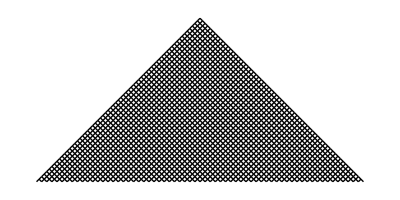
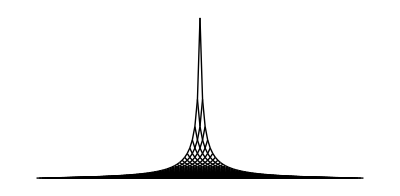
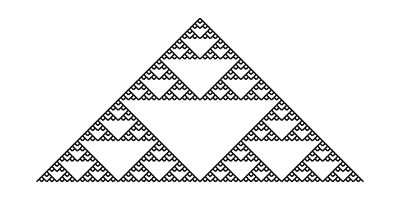
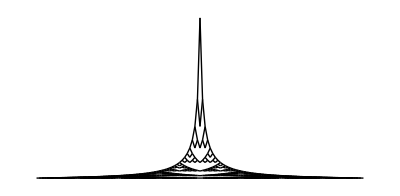
{{-Graphics-⋮,-Graphics-},{-Graphics-⋮,-Graphics-}}

```mathematica
Table[{Framed@Labeled[Graphics[lines,],"⋮"],Framed@Graphics[Replace[lines,{x_,t_}->{x/64,-1+1/(1-t)},{-2}]]},{lines,{NestList[Flatten[{Line[{#,#+{1,-1}}],Line[{#,#+{-1,-1}}]}&/@With[{w=#⟦1,2⟧&/@#},Union[w]],1]&,{Line[{{0,0},{-1,-1}}],Line[{{0,0},{1,-1}}]},64-1],NestList[Flatten[{Line[{#,#+{1,-1}}],Line[{#,#+{-1,-1}}]}&/@With[{w=#⟦1,2⟧&/@#},Select[Union[w],OddQ[Count[w,#]]&]],1]&,{Line[{{0,0},{-1,-1}}],Line[{{0,0},{1,-1}}]},64-1]}}]
```